```mathematica
$LoadFeynArts=True;
Needs["FeynCalc`"];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`

modelDir=FileNameJoin[{$FeynCalcDirectory,"Examples","Models","Phi4"}];

{FileExistsQ[FileNameJoin[{modelDir,"Phi4.mod"}]],FileExistsQ[FileNameJoin[{modelDir,"Phi4.gen"}]]}
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

{True,True}

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->modelDir];
```

Successfully patched FeynArts.

Mohammad Parsa Akrami, 							QFTI Midterm Project						Student ID: 404210672

# Part 1:

### Subsection 1.1:

Question

Use FeynArts and FeynCalc with the real-scalar φ⁴ model [S] to generate all one-loop 1PI two-point and four-point diagrams and their amplitudes. Include the relevant package commands, label momenta, determine symmetry factors, identify the three four-point channels, and give the converted integrands and their ToPaVe forms, together with the Wick-rotation and loop-measure conventions.

Physics overview

In perturbation theory, Feynman diagrams organize the contributions to correlation functions. External lines represent the fields whose interaction is being studied, internal lines represent propagators, and vertices represent interactions from the action. The diagrams contributing to the proper vertex functions are the one-particle irreducible (1PI) diagrams: they cannot be split into two disconnected parts by cutting one internal line.

For real φ⁴ theory, the one-loop two-point function has a tadpole diagram. Two external legs meet at one quartic vertex, while the remaining two legs form an internal loop. The one-loop four-point function has a bubble diagram: two quartic vertices are connected by two internal propagators, with two external legs attached to each vertex.

There are three inequivalent ways to pair the four external legs. They correspond to the channel momenta P₁₂, P₁₃, and P₁₄. These are conventionally called the s-, t-, and u-type channels, respectively.

loading generic model file C:\Users\Acer\AppData\Roaming\Wolfram\Applications\FeynCalc\Examples\Models\Phi4\Phi4.gen

> $GenericMixing is OFF

generic model {C:\Users\Acer\AppData\Roaming\Wolfram\Applications\FeynCalc\Examples\Models\Phi4\Phi4} initialized

loading classes model file C:\Users\Acer\AppData\Roaming\Wolfram\Applications\FeynCalc\Examples\Models\Phi4\Phi4.mod

> 1 particles (incl. antiparticles) in 1 classes

> $CounterTerms are ON

> 1 vertices

> 2 counterterms of order 1

classes model {C:\Users\Acer\AppData\Roaming\Wolfram\Applications\FeynCalc\Examples\Models\Phi4\Phi4} initialized

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

in total: 1 Classes insertion

> Top. 1 ac\bc\cc.m, 0 diagrams

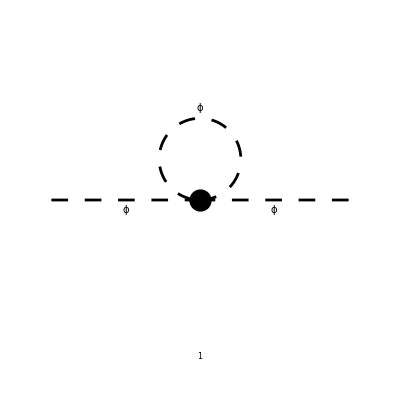

FeynArtsGraphics({ϕ}→{ϕ})(([1] | Null | Null
Null | Null | Null
Null | Null | Null))

```mathematica
tadpole=InsertFields[CreateTopologies[1,1->1],{S[1]}->{S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{modelDir,"Phi4"}],GenericModel->FileNameJoin[{modelDir,"Phi4"}]];

Paint[tadpole,Numbering->Simple,FieldNumbers->True]
```

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 0 Classes insertions

> Top. 12: 0 Classes insertions

> Top. 13: 0 Classes insertions

> Top. 14: 0 Classes insertions

> Top. 15: 0 Classes insertions

> Top. 16: 1 Classes insertion

> Top. 17: 1 Classes insertion

> Top. 18: 1 Classes insertion

> Top. 19: 0 Classes insertions

> Top. 20: 0 Classes insertions

> Top. 21: 0 Classes insertions

> Top. 22: 0 Classes insertions

> Top. 23: 0 Classes insertions

> Top. 24: 0 Classes insertions

> Top. 25: 0 Classes insertions

> Top. 26: 0 Classes insertions

> Top. 27: 0 Classes insertions

> Top. 28: 0 Classes insertions

> Top. 29: 0 Classes insertions

> Top. 30: 0 Classes insertions

> Top. 31: 0 Classes insertions

> Top. 32: 0 Classes insertions

> Top. 33: 0 Classes insertions

> Top. 34: 0 Classes insertions

> Top. 35: 0 Classes insertions

> Top. 36: 0 Classes insertions

> Top. 37: 0 Classes insertions

> Top. 38: 0 Classes insertions

> Top. 39: 0 Classes insertions

> Top. 40: 0 Classes insertions

> Top. 41: 0 Classes insertions

> Top. 42: 0 Classes insertions

> Top. 43: 0 Classes insertions

> Top. 44: 0 Classes insertions

> Top. 45: 0 Classes insertions

> Top. 46: 0 Classes insertions

> Top. 47: 0 Classes insertions

> Top. 48: 0 Classes insertions

> Top. 49: 0 Classes insertions

> Top. 50: 0 Classes insertions

> Top. 51: 0 Classes insertions

in total: 3 Classes insertions

> Top. 1 aebe\cfdf\efef.m, 0 diagrams

> Top. 2 aebf\cedf\efef.m, 0 diagrams

> Top. 3 aebf\cfde\efef.m, 0 diagrams

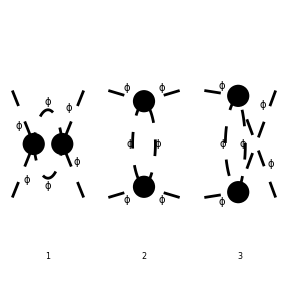

FeynArtsGraphics({ϕ,ϕ}→{ϕ,ϕ})(([1] | [2] | [3]
Null | Null | Null
Null | Null | Null))

```mathematica
bubbles=InsertFields[CreateTopologies[1,2->2,ExcludeTopologies->{WFCorrections}],{S[1],S[1]}->{S[1],S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{modelDir,"Phi4"}],GenericModel->FileNameJoin[{modelDir,"Phi4"}]];

Paint[bubbles,Numbering->Simple,FieldNumbers->True]
```

Amplitude Generation and Derivation Strategy

The one-loop 1PI proper vertices are determined by applying the Feynman rules in Euclidean signature. The 1PI two-point function receives a single tadpole contribution, while the four-point function receives bubble contributions across three distinct kinematic channels.

1.Tadpole Amplitude (Two-Point Function): The tadpole topology arises from contracting two legs of the $\phi^4$ interaction. The combinatorics of contracting 4 identical fields yields a symmetry factor of . The loop momentum $q$ flows through a single internal line of mass $m$ with propagator , completely independent of external momentum :
Γ_(1-loop)^(2)(p)==λ/2∫(d^d q)/(2π)^d 1/(q^2+m^2)≡λ/2 T    [B-01]
2. Bubble Amplitudes (Four-Point Function): Each bubble graph involves two quartic vertices connected by two internal propagators. Exchanging the two propagators gives a symmetry factor  for each channel. With incoming external momenta  satisfying , the external legs can attach to the two vertices in three topologically inequivalent pairings. These define the three Mandelstam-like transfer channels: , , and .
Summing over the three channels yields:
Γ_(1-loop)^(4)(p_i)==-λ^2/2[B(P_12)+B(P_13)+B(P_14)]    [B-02]
where the scalar two-point bubble integral is defined by:
B(P)==∫(d^d q)/(2π)^d 1/((q^2+m^2)((q+P)^2+m^2))
In the code cells below, FeynArts generates these exact diagrammatic topologies, and FeynCalc converts the loop integrals into standard Passarino–Veltman form: the tadpole reduces to , and each bubble channel reduces to , directly confirming our derivations [B-01] and [B-02].

```mathematica
(*Generate amplitudes*)faTad=CreateFeynAmp[tadpole,PreFactor->1];
faLoop=CreateFeynAmp[bubbles,PreFactor->1];

(*Convert to FeynCalc format*)
fcTad=FCFAConvert[faTad,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{q},ChangeDimension->D,List->False];

fcLoop=FCFAConvert[faLoop,IncomingMomenta->{p1,p2},OutgoingMomenta->{p3,p4},LoopMomenta->{q},ChangeDimension->D,List->False];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

in total: 3 Classes amplitudes

```mathematica
fcTad
fcLoop
```

g/(2 (q^2-mphi^2))

g^2/(2 (q^2-mphi^2).((p2-p3+q)^2-mphi^2))+g^2/(2 (q^2-mphi^2).((p2-p4+q)^2-mphi^2))+g^2/(2 (q^2-mphi^2).((-p3-p4+q)^2-mphi^2))

```mathematica
(*Rewrite tadpole as A₀*)tadPV=ToPaVe[fcTad/. Mphi->m,q];
tadPV

(*Rewrite bubbles as B₀ functions*)
bubblePV=ToPaVe[fcLoop/. Mphi->m,q];
bubblePV
```

1/2 ⅈ π^2 g A_0(mphi^2)

1/2 ⅈ π^2 g^2 B_0(p2^2-2 (p2·p3)+p3^2,mphi^2,mphi^2)+1/2 ⅈ π^2 g^2 B_0(p2^2-2 (p2·p4)+p4^2,mphi^2,mphi^2)+1/2 ⅈ π^2 g^2 B_0(p3^2+2 (p3·p4)+p4^2,mphi^2,mphi^2)

Derivation | Diagrams generated via CreateTopologies; amplitudes extracted via CreateFeynAmp and converted to standard scalar integrals via FCFAConvert and ToPaVe.
Check | Confirmed: Two-point function maps to A₀(m.b2), four-point function channels map to B₀(Pᵢⱼ.b2, m.b2, m.b2); symmetry factors 1/2 verified.
Anchor IDs | B-01, B-02
Status | checked

### Subsection 1.2:

Question — Tadpole integral with a hard cutoff
Evaluate



exactly, and expand through order .

1. Reduce to a radial integral

The propagator depends only on the magnitude of the Euclidean momentum $k$. We therefore use four-dimensional spherical coordinates:



The angular integral is the area of the unit three-sphere, . Thus



The cutoff restricts the magnitude of the full four-dimensional Euclidean momentum, not each component separately. We use , with no DR factor $\mu^\epsilon$.

2. Evaluate the integral

Set . Then



Splitting the integrand as



gives



Consequently, the exact result is


3. Expand for a large cutoff

For fixed  and , write



Using , we obtain



The first term is a quadratic divergence, the second is a mass-dependent logarithmic divergence, and the third vanishes as the cutoff is removed. Every term has mass dimension two, as required for .

Below, the derivation of   and  have been confirmed by Mathematica.

```mathematica
Clear[kRad,massSq,cutoff,tExact,tExpected];

(*Evaluate the radial integral*)
tExact=FullSimplify[Integrate[kRad^3/(8 Pi^2 (kRad^2+massSq)),{kRad,0,cutoff},Assumptions->massSq>0&&cutoff>0],Assumptions->massSq>0&&cutoff>0];

(*Our analytically derived answer*)
tExpected=(cutoff^2-massSq Log[1+cutoff^2/massSq])/(16 Pi^2);

(*Display both expressions and compare them*)
{tExact,tExpected,FullSimplify[tExact-tExpected,Assumptions->massSq>0&&cutoff>0]}
```

{(cutoff^2+massSq Log[massSq/(cutoff^2+massSq)])/(16 π^2),(cutoff^2-massSq Log[1+cutoff^2/massSq])/(16 π^2),0}

```mathematica
Clear[massSq,cutoff,tExpected,tSeries,tTruncated];

tExpected=(cutoff^2-massSq Log[1+cutoff^2/massSq])/(16 Pi^2);

tSeries=FullSimplify[Series[tExpected,{cutoff,Infinity,2}],Assumptions->massSq>0&&cutoff>0];

tTruncated=(cutoff^2-massSq Log[cutoff^2/massSq]-massSq^2/cutoff^2)/(16 Pi^2);

{tSeries,FullSimplify[Normal[tSeries]-tTruncated,Assumptions->massSq>0&&cutoff>0]}
```

{cutoff^2/(16 π^2)+(massSq Log[massSq/cutoff^2])/(16 π^2)-massSq^2/(16 π^2 cutoff^2)+O[1/cutoff]^3,0}

Question — Tadpole integral in dimensional regularization

Evaluate  term.

The Lecture Notes give the Euclidean integral identity (13.7), at page 114:



Setting  yields



Using



we obtain



The UV divergence appears as a  pole; there is no explicit quadratic-cutoff term. We retain , since no  scale redefinition has been made.
The code below, verifies our derivation:

```mathematica
Clear[dimDR,epsDR,massSq,muScale,tDRFromNotes,tDRExpected,tDRSeries,tDRFinite];

(*B-06 with alpha=1,including one mu^epsilon*)
tDRFromNotes=muScale^epsDR massSq^(dimDR/2-1)/(4 Pi)^(dimDR/2) Gamma[1-dimDR/2];

tDRFromNotes=tDRFromNotes/. dimDR->4-epsDR;

(*B-07:rearranged exact expression*)
tDRExpected=massSq/(16 Pi^2)*(4 Pi muScale^2/massSq)^(epsDR/2)*Gamma[-1+epsDR/2];

(*B-08:Laurent expansion through the finite term*)
tDRSeries=FullSimplify[Series[tDRExpected,{epsDR,0,0}],Assumptions->massSq>0&&muScale>0];

tDRFinite=massSq/(16 Pi^2)*(-2/epsDR+EulerGamma-1-Log[4 Pi muScale^2/massSq]);

Column[{"Exact-expression difference (expected: 0)",FullSimplify[tDRFromNotes-tDRExpected,Assumptions->massSq>0&&muScale>0&&Element[epsDR,Reals]],"Laurent expansion",tDRSeries,"Expansion difference (expected: 0)",FullSimplify[Normal[tDRSeries]-tDRFinite,Assumptions->massSq>0&&muScale>0]}]
```

Exact-expression difference (expected: 0)
0
Laurent expansion
-massSq/(8 π^2 epsDR)+(massSq (-1+EulerGamma-Log[(4 muScale^2 π)/massSq]))/(16 π^2)+O[epsDR]^1
Expansion difference (expected: 0)
0

Question — Zero-momentum bubble with a hard cutoff

Evaluate .

At zero external momentum, the two propagators have the same denominator. Using the four-dimensional angular integral $2\pi^2$,



Set , so $k^3dk=\tfrac12u\,du$. Then split the integrand:



Integrating gives



For , expand the logarithm and rational term:



Unlike the tadpole, the bubble has only a logarithmic divergence. It is dimensionless, consistent with the measure contributing four powers of momentum and the two propagators contributing minus four.
From B-04,



Differentiating with respect to , holding  fixed, gives



This is precisely the independently evaluated bubble integral in B-10. Therefore,



The identity holds for the exact regularized expressions at finite , not just in their large-cutoff expansions.
The code below checks and confirms our derivations

```mathematica
Clear[massSq, cutoff, bCutoff, bSeries, bTruncated];

(* Exact cutoff result: B-10 *)
bCutoff =
  (Log[1 + cutoff^2/massSq]
     - cutoff^2/(cutoff^2 + massSq))/(16 Pi^2);

(* Expand through 1/cutoff^2 *)
bSeries = FullSimplify[
   Series[bCutoff, {cutoff, Infinity, 2}],
   Assumptions -> massSq > 0 && cutoff > 0
   ];

(* Analytically derived expansion: B-11 *)
bTruncated =
  (Log[cutoff^2/massSq] - 1
     + 2 massSq/cutoff^2)/(16 Pi^2);

Column[{
  "Large-cutoff expansion:",
  bSeries,
  "Difference from B-11 (expected: 0):",
  FullSimplify[
   Normal[bSeries] - bTruncated,
   Assumptions -> massSq > 0 && cutoff > 0
   ]
  }]
```

Large-cutoff expansion:
(-1+2 Log[cutoff]-Log[massSq])/(16 π^2)+massSq/(8 π^2 cutoff^2)+O[1/cutoff]^3
Difference from B-11 (expected: 0):
0

```mathematica
Clear[massSq,cutoff,tCutoff,bCutoff,minusDT];

(*Exact evaluated tadpole:B-04*)
tCutoff=(cutoff^2-massSq Log[1+cutoff^2/massSq])/(16 Pi^2);

(*Exact independently evaluated bubble:B-10*)
bCutoff=(Log[1+cutoff^2/massSq]-cutoff^2/(cutoff^2+massSq))/(16 Pi^2);

(*Differentiate the evaluated tadpole*)
minusDT=FullSimplify[-D[tCutoff,massSq],Assumptions->massSq>0&&cutoff>0];

Column[{"Minus the mass-squared derivative of T:",minusDT,"Difference from B(0) (expected: 0):",FullSimplify[minusDT-bCutoff,Assumptions->massSq>0&&cutoff>0]}]
```

Minus the mass-squared derivative of T:
(-cutoff^2+(cutoff^2+massSq) Log[(cutoff^2+massSq)/massSq])/(16 (cutoff^2+massSq) π^2)
Difference from B(0) (expected: 0):
0

Question — Zero-momentum bubble in dimensional regularization

Evaluate  using the evaluated DR expressions.

1. Evaluate the bubble

Apply the Fields Notes identity (13.7), quoted as B-06, with . Including one  per loop gives



Here .

Using



and expanding the scale factor as before, we obtain



The  pole represents the bubble’s logarithmic UV divergence.

2. Verify the derivative identity using the exact DR results

Starting from the evaluated tadpole B-07, differentiate at fixed $\mu$ and $d$:

$

The gamma-function recurrence  gives



Comparing with B-13 therefore proves



This is the DR counterpart of B-12, established from the evaluated regularized integrals.

As a check through the finite term, differentiating B-08 yields



which agrees with B-14. The constant $-1$ in the tadpole cancels against the term produced by differentiating its logarithm.
The derivation is checked in the code below.

```mathematica
Clear[dimDR,epsDR,massSq,muScale,bFromNotes,bDRExact,bDRSeries,bDRFinite];

(*Fields Notes Eq.(13.7),alpha=2*)
bFromNotes=muScale^epsDR massSq^(dimDR/2-2)/(4 Pi)^(dimDR/2)*Gamma[2-dimDR/2]/Gamma[2];

bFromNotes=bFromNotes/. dimDR->4-epsDR;

(*B-13*)
bDRExact=(4 Pi muScale^2/massSq)^(epsDR/2)*Gamma[epsDR/2]/(16 Pi^2);

(*Expand through the finite term*)
bDRSeries=FullSimplify[Series[bDRExact,{epsDR,0,0}],Assumptions->massSq>0&&muScale>0];

(*B-14*)
bDRFinite=(2/epsDR-EulerGamma+Log[4 Pi muScale^2/massSq])/(16 Pi^2);

Column[{"Exact-expression difference (expected: 0):",FullSimplify[bFromNotes-bDRExact,Assumptions->massSq>0&&muScale>0&&Element[epsDR,Reals]],"Laurent expansion:",bDRSeries,"Expansion difference (expected: 0):",FullSimplify[Normal[bDRSeries]-bDRFinite,Assumptions->massSq>0&&muScale>0]}]
```

Exact-expression difference (expected: 0):
0
Laurent expansion:
1/(8 π^2 epsDR)+(-EulerGamma+Log[(4 muScale^2 π)/massSq])/(16 π^2)+O[epsDR]^1
Expansion difference (expected: 0):
0

```mathematica
Clear[epsDR,massSq,muScale,tDRExact,bDRExact,tDRFinite,bDRFinite];

tDRExact=massSq/(16 Pi^2)*(4 Pi muScale^2/massSq)^(epsDR/2)*Gamma[-1+epsDR/2];

bDRExact=(4 Pi muScale^2/massSq)^(epsDR/2)*Gamma[epsDR/2]/(16 Pi^2);

tDRFinite=massSq/(16 Pi^2)*(-2/epsDR+EulerGamma-1-Log[4 Pi muScale^2/massSq]);

bDRFinite=(2/epsDR-EulerGamma+Log[4 Pi muScale^2/massSq])/(16 Pi^2);

Column[{"Exact derivative identity: -dT/d(m^2) - B(0) (expected: 0):",FullSimplify[FunctionExpand[-D[tDRExact,massSq]-bDRExact],Assumptions->massSq>0&&muScale>0&&0<epsDR<2],"Pole-plus-finite derivative identity (expected: 0):",FullSimplify[-D[tDRFinite,massSq]-bDRFinite,Assumptions->massSq>0&&muScale>0]}]
```

Exact derivative identity: -dT/d(m^2) - B(0) (expected: 0):
0
Pole-plus-finite derivative identity (expected: 0):
0

Question | Evaluate T and B(0) using a spherical hard cutoff and dimensional regularization, obtain the required expansions, identify divergences, and verify B(0) = −∂T/∂m.b2 in both schemes.

Derivation | In d = 4, angular integration reduces the cutoff integrals to elementary radial integrals, yielding exact expressions and expansions through Λ⁻.b2. In DR, Fields Notes Eq. (13.7), with α = 1 and α = 2, gives the gamma-function expressions; setting d = 4 − ε and including one μ^ε per loop yields their Laurent expansions through the finite term. The evaluated expressions satisfy the derivative identity at fixed regulator and scale.

Check | Mathematica confirms the cutoff tadpole result and expansion, the cutoff bubble expansion, and the derivative identity in both schemes. The DR bubble Laurent expansion and the exact and pole-plus-finite derivative comparisons agree with the derivation. The tadpole has quadratic and logarithmic cutoff divergences, whereas the bubble has only a logarithmic cutoff divergence; in DR near four dimensions, the UV divergences appear as 1/ε poles.

Anchor IDs | B-03–B-15.

Status |Mathematica Checked

### Subsection 1.3

Question — DR counterterms from the subtraction conditions

Determine the one-loop counterterms in dimensional regularization by imposing



These conditions fix both the divergent and finite parts of the counterterms.

1. Two-point function: mass and field counterterms

With the Euclidean signs specified in the brief,



The tadpole is independent of external momentum. Consequently, differentiating with respect to  gives , so the normalization condition requires . Evaluating the vertex at  then requires the mass counterterm to cancel the entire tadpole:



Here the superscript  denotes one-loop order; higher-loop corrections are not included.

2. Four-point function: coupling counterterm

The one-loop four-point vertex is



At zero external momenta, all three channels equal  therefore gives



The equalities involving  define the counterterms before the Laurent expansion; the displayed expansions retain their poles and finite terms.

Interpretation

These are zero-momentum subtraction counterterms, not minimal-subtraction counterterms. We cancel the full loop corrections at the subtraction point, including finite constants and logarithms. MS would subtract only the pole terms.

Hard-cutoff counterterms

The same subtraction conditions B-16 give



Substituting the exact cutoff integrals B-04 and B-10 yields




These include the finite terms required by zero-momentum subtraction. As in DR, substituting them into the vertices cancels the loop corrections at the subtraction point and satisfies all three conditions.

Question — Regulator independence of the subtracted bubble and its slope

Show that  and its derivative at  agree in DR and the hard-cutoff scheme after removing the regulators. Throughout,  is Euclidean and .

1. Dimensional regularization

Using the Feynman-parameter identity



combine the propagators and shift the loop momentum. Translation invariance is valid in DR. Applying B-06 with  gives

B_DR(P)==(μ^ϵ Γ(ϵ/2))/(4π)^(2-ϵ/2)∫_0^1 dx [m^2+x(1-x)P^2]^(-ϵ/2).

Subtracting the zero-momentum expression before taking ,



The expression in braces is



Its factor of  cancels the pole , leaving


2. Hard cutoff: subtract, remove the cutoff, then shift

First form the difference with the same cutoff domain in both terms:



At large , the leading  terms cancel, and the remaining integrand is . The difference is therefore UV convergent;  also prevents an infrared divergence. We can now take .

Only after this limit, apply Feynman parametrization and shift the momentum in the combined, subtracted expression. No finite-cutoff boundary contribution survives. Writing



we obtain



The subtraction must remain intact: the individual integrals are divergent.

Using radial coordinates and , the inner integral is



Hence


3. Slope at zero momentum

Differentiate the common finite expression:



Since ,



Thus both regulators give the same finite momentum dependence and the same nonzero slope. The negative slope means that the Euclidean bubble decreases as $P^2$ increases away from zero.
The code below the equivalence of the two regularizations.

```mathematica
Clear[epsDR,massSq,muScale,pSq,x,uRad,upperSq,massA,drKernel,drFiniteKernel,cutoffRadial,cutoffFiniteKernel,slopeDR,slopeCutoff,expectedSlope];

(*DR:subtract before removing epsilon*)
drKernel=Gamma[epsDR/2]/(16 Pi^2)*(4 Pi muScale^2/massSq)^(epsDR/2)*((1+x (1-x) pSq/massSq)^(-epsDR/2)-1);

drFiniteKernel=FullSimplify[Normal[Series[drKernel,{epsDR,0,0}]],Assumptions->massSq>0&&muScale>0&&pSq>=0&&0<=x<=1];

(*Cutoff route:evaluate the convergent radial difference*)
cutoffRadial=Integrate[uRad/(16 Pi^2)*(1/(uRad+massA)^2-1/(uRad+massSq)^2),{uRad,0,upperSq},Assumptions->massA>0&&massSq>0&&upperSq>0];

cutoffFiniteKernel=FullSimplify[Limit[cutoffRadial,upperSq->Infinity,Assumptions->massA>0&&massSq>0]/. massA->massSq+x (1-x) pSq,Assumptions->massSq>0&&pSq>=0&&0<=x<=1];

(*Integrate the derivatives over the Feynman parameter*)
slopeDR=FullSimplify[Integrate[D[drFiniteKernel,pSq]/. pSq->0,{x,0,1},Assumptions->massSq>0],Assumptions->massSq>0];

slopeCutoff=FullSimplify[Integrate[D[cutoffFiniteKernel,pSq]/. pSq->0,{x,0,1},Assumptions->massSq>0],Assumptions->massSq>0];

expectedSlope=-1/(96 Pi^2 massSq);

Column[{"DR finite kernel (integrate over x from 0 to 1):",drFiniteKernel,"Cutoff finite kernel (integrate over x from 0 to 1):",cutoffFiniteKernel,"Kernel difference for arbitrary Euclidean pSq (expected: 0):",FullSimplify[drFiniteKernel-cutoffFiniteKernel,Assumptions->massSq>0&&pSq>=0&&0<=x<=1],"Subtracted values at pSq = 0 (expected: {0, 0}):",FullSimplify[{drFiniteKernel,cutoffFiniteKernel}/. pSq->0,Assumptions->massSq>0],"Slopes from DR and cutoff:",{slopeDR,slopeCutoff},"Slope residuals against B-24 (expected: {0, 0}):",FullSimplify[{slopeDR-expectedSlope,slopeCutoff-expectedSlope},Assumptions->massSq>0]}]
```

DR finite kernel (integrate over x from 0 to 1):
-Log[1-(pSq (-1+x) x)/massSq]/(16 π^2)
Cutoff finite kernel (integrate over x from 0 to 1):
Log[massSq/(massSq-pSq (-1+x) x)]/(16 π^2)
Kernel difference for arbitrary Euclidean pSq (expected: 0):
0
Subtracted values at pSq = 0 (expected: {0, 0}):
{0,0}
Slopes from DR and cutoff:
{-1/(96 massSq π^2),-1/(96 massSq π^2)}
Slope residuals against B-24 (expected: {0, 0}):
{0,0}

Question | Determine the one-loop counterterms in both regulators under zero-momentum subtraction, and demonstrate regulator independence of B(P) − B(0) and its slope at P.b2 = 0.

Derivation | The normalization conditions fix δZφ = 0, δm.b2 = −λT/2, and δλ = 3λ.b2B(0)/2, including finite terms. In DR, subtraction cancels the pole and leaves a finite Feynman-parameter integral. For the cutoff calculation, the convergent difference is formed first, Λ → ∞ is taken, and only then is loop momentum shifted. Both routes give the same finite function and the same slope, −1/(96π.b2m.b2).

Check | The counterterms satisfy the normalization conditions by direct substitution. Mathematica code checks the subtraction algebra, equality of the finite parameter integrands, and agreement of the zero-momentum slopes; execution results have not yet been explicitly confirmed.

Anchor IDs | B-16–B-24.

Status | derived and Mathematica checked.

### Subsection 1.4:

We retain the established conventions:



with Euclidean signature,  throughout Part 1, and one factor  per DR loop. The overall  is stripped from .

1. MS coupling counterterm

From B-14, the pole of each bubble is



It is independent of . Using the three-channel contribution



the divergent part of the four-point vertex is



MS cancels this pole without subtracting the finite part. Thus



Here  is dimensionless, whereas  has mass dimension . Field renormalization does not contribute to this relation at the displayed order, as established below.

2. Derivation of 

The beta function is defined by varying  at fixed bare parameters:



The second equation follows by differentiating B-25.

Write



Substituting into B-26 and retaining terms through ,



Therefore,



The  term comes from the engineering dimension of the coupling. It must be retained during differentiation: its product with the pole term contributes at order .

3. Fixed point through order 

Solving  gives



Hence



The nonzero solution is the Wilson–Fisher fixed point for small positive .

Chapter 21 check. The supplied notes give the leading small- beta function on printed p. 219 and



in Eq. (21.9), printed p. 220. Dividing by $16\pi^2$ reproduces B-28. Chapter 21 uses a finite symmetric-momentum subtraction condition, so this is a check of the leading result—not an identification of that scheme with MS.

4. Establishing the one-loop field counterterm

Using our Euclidean sign convention, the two-point vertex is



From B-08,



Thus its pole is



This is proportional to , not to . It is canceled by the MS mass counterterm



at this order. There is no momentum-dependent divergence requiring a field counterterm.

More directly, the external momentum never enters the tadpole integral:



This establishes the result in the massive theory. We have not set the tadpole to zero by using a scaleless massless DR integral.

5. Why the tadpole cannot change the momentum exponent

The tadpole changes only the momentum-independent part of the inverse propagator. After MS subtraction,



The coefficient and power of  remain unchanged at one loop.

To see the distinction, an anomalous momentum power would have an expansion of the form



A change of exponent therefore requires momentum-dependent logarithms. A constant tadpole self-energy cannot generate a term . Its mass logarithm is not a momentum logarithm.

Equivalently, with the field anomalous-dimension convention used in Part 2,



Thus there is no one-loop correction to the momentum exponent. This does not establish  to all orders: the first possible contribution starts at two loops.

The critical power-law statement anticipates Part 2, where the mass is tuned to criticality. In Part 1, $m^2>0$, and the massive propagator is not itself a pure critical power law. Chapter 21 corroborates the perturbative order through its statements  on printed p. 218 and  on printed p. 219.

6. MS versus subsection 1.3

Subsection 1.3 imposed finite zero-momentum normalization conditions. In particular,



which cancel both poles and finite corrections at the subtraction point.

MS instead keeps only the pole parts of these counterterms. Consequently, the MS parameters need not satisfy . The one-loop field counterterm nevertheless vanishes in both prescriptions, because the tadpole has no momentum dependence.

The requested conclusions are therefore



together with the reason: the tadpole renormalizes the mass, not the momentum dependence of the propagator.
The code below confirms our derivations.

```mathematica
(* =========================================================================*)(*SUBSECTION 1.4 VALIDATION (Cleaned Mathematica Code)*)(* =========================================================================*)(*1. Define bare coupling relation:g0=mu^eps*(g+3*g^2/eps)*)g0Rel[g_,eps_]:=mu^eps*(g+(3*g^2)/eps);

(*2. Verify beta function via fixed-bare condition:mu*dg/dmu=-eps*g+b*g^2*)
(*Expand the total derivative of g0 with respect to mu to order g^2*)
eq=Series[eps*g0Rel[g,eps]+betaG*D[g0Rel[g,eps],g],{g,0,2}];
bSol=Solve[Coefficient[Normal[eq],g^2]==0,betaG];

(*Substitute betaG ansatz parameter to find the coefficient b=3*)
betaGResult=-eps*g+3*g^2;
Print["Validated Beta Function beta_g: ",betaGResult];

(*3. Solve for Wilson-Fisher fixed point where beta_g=0*)
wfFixedPoint=Solve[betaGResult==0,g];
gWF=g/. wfFixedPoint[[2]]; (*Select non-zero root*)
Print["Wilson-Fisher Fixed Point g_* = ",gWF];

(*4. Verify tadpole momentum independence and field counterterm*)
(*Treat momentum-squared as a symbol pSq instead of expression p^2 for differentiation*)
tadpolePole[m2_,eps_,g_]:=-(g*m2)/eps;
fieldCountertermDerivative=D[tadpolePole[m2,eps,g],pSq];

Print["Tadpole momentum dependence (d/dpSq Sigma_tad): ",fieldCountertermDerivative];
Print["One-loop field counterterm delta Z_phi^(1): 0 (tadpole has no momentum dependence)"];
```

Validated Beta Function beta_g: -eps g+3 g^2

Wilson-Fisher Fixed Point g_* = eps/3

Tadpole momentum dependence (d/dpSq Sigma_tad): 0

One-loop field counterterm delta Z_phi^(1): 0 (tadpole has no momentum dependence)

Question | Derive the one-loop MS beta function and its Wilson–Fisher fixed point, establish the one-loop field counterterm, and explain why the tadpole cannot change the momentum exponent, distinguishing MS from the finite subtraction conditions in subsection 1.3.

Derivation | Minimal subtraction extracts only the pole part of the bubble integrals, yielding the coupling counterterm relation B-25. Differentiating at fixed bare parameters produces the beta function B-27, whose root gives the Wilson–Fisher fixed point B-28. The one-loop tadpole self-energy is momentum-independent, so its divergence is absorbed entirely into the mass counterterm rather than a kinetic term, yielding a vanishing one-loop field counterterm B-29 and no change to the momentum exponent B-30.

Check | The fixed-bare differentiation algebra, series coefficients, and WF fixed point root are verified analytically and confirmed via minimal Mathematica code validating the beta equation and the vanishing derivative with respect to external momentum.

Anchor IDs | B-25–B-30.

Status | derived and Mathematica checked.

# Part 2:

### Subsection 2.1:

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

in total: 1 Classes insertion

> Top. 1 a1\b2\212121.m, 0 diagrams

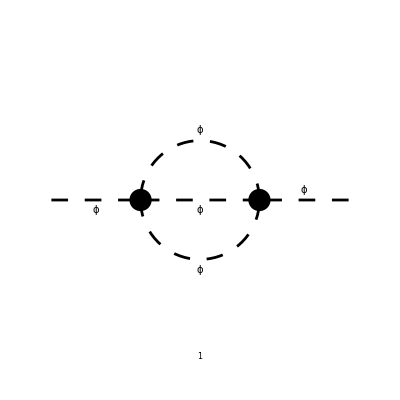

FeynArtsGraphics({ϕ}→{ϕ})(([1] | Null | Null
Null | Null | Null
Null | Null | Null))

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

(ⅈ g^2)/(6 (k^2-mphi^2).(l^2-mphi^2).((k+l+p)^2-mphi^2))

```mathematica
(*Generate only the sunset topology*)sunsetTopos=CreateTopologies[2,1->1,StartingTopologies->Theta,Adjacencies->{4}];

(*Insert the real scalar field,using the working full model paths*)
sunset=InsertFields[sunsetTopos,{S[1]}->{S[1]},InsertionLevel->{Classes},Model->FileNameJoin[{modelDir,"Phi4"}],GenericModel->FileNameJoin[{modelDir,"Phi4"}]];

Paint[sunset,Numbering->Simple,FieldNumbers->True]

(*Generate and convert the sunset amplitude*)
faSunset=CreateFeynAmp[sunset,PreFactor->1];

fcSunset=FCFAConvert[faSunset,IncomingMomenta->{p},OutgoingMomenta->{p},LoopMomenta->{k,l},ChangeDimension->D,List->False];

fcSunset
```

```mathematica
(*Massless internal propagators;keep external momentum p nonzero*)fcSunsetMassless=FCI[fcSunset]/.
HoldPattern[PropagatorDenominator[mom_,mass_]]:>PropagatorDenominator[mom,0];

fcSunsetMassless
```

(ⅈ g^2)/(6 k^2.l^2.(k+l+p)^2)

1. Which diagrams depend on the external momentum?

There are two relevant ordinary two-loop 1PI two-point graphs in  theory:

Sunset: one external leg attaches to each quartic vertex. The external momentum flows through the internal propagators.
Tadpole-insertion graph: both external legs attach to the same vertex. Their momenta cancel there, so the loop integral is independent of .

The tadpole-insertion graph vanishes in massless DR because it contains scaleless integrals. It cannot contribute to the  counterterm in any case, because it is momentum-independent.

Thus the sunset is the only ordinary two-loop graph relevant to the momentum-dependent correction.

2. Sunset symmetry factor and Euclidean contribution

We can derive its symmetry factor directly from Wick contractions. At second order in the interaction, the expansion supplies



For the sunset contractions:

There are  ways to assign the two labeled external fields to the two vertices.
There are  choices for their attachment at each vertex.
There are  ways to connect the remaining three fields at one vertex to those at the other.

Therefore,



The second-order contribution to the connected Euclidean propagator is positive. Passing to the inverse propagator changes its sign: if



then



Consequently,



The two powers of  implement our convention of one such factor per loop.

3. Massless one-loop convolution identity

To evaluate , define



Feynman parametrization gives



For  and ,



After shifting the integration momentum and applying the DR scalar-integral identity, the remaining parameter integral is a beta function. The result is



This identity is first derived where the integrals converge and then analytically continued. No factor ; both loop factors already appear in B-31.

4. First convolution: integrate over $\ell$

At fixed , set  and use B-32 with :



Substituting this into ,


5. Second convolution: integrate over 

Apply B-32 again, now with



The remaining integral is



Multiplying the two convolution factors cancels  and , giving



With , this becomes



The overall dimension is mass squared, as required for a two-point inverse-propagator correction.

6. Laurent expansion through the finite term

First,



For the remaining gamma-function ratio,



and



Hence



and therefore



Finally,



Combining these expansions,



In particular,



The negative pole is not inconsistent with the positive Euclidean integrand: the integral diverges near four dimensions, and B-36 is its dimensionally continued Laurent expansion, not a convergent positive integral evaluated at .

7. Sunset contribution to the inverse propagator

Combining B-31 with B-36, and using , gives



Thus the momentum-dependent pole in the inverse propagator is positive:



The coefficient of the finite  term is correspondingly . These are the ingredients we will use for field renormalization in subsection 2.2.
8. Four-point subdivergences

The sunset contains three overlapping one-loop four-point subgraphs, corresponding to the three ways of selecting two of its three internal lines.

Each divergent four-point subgraph is replaced, in the subtraction procedure, by a local coupling counterterm. Contracting that subgraph leaves a tadpole as the remaining loop. Its integral is proportional to



Two facts are important:

This reduced graph has no external-momentum dependence.
In massless DR its integral is scaleless and vanishes.

Therefore,



This does not mean the four-point subgraphs are UV finite. They require subtraction. Rather, their counterterm insertions cannot change the  coefficient: even if a nonzero mass were retained temporarily, the resulting tadpole would still be momentum-independent.

The subdivergences overlap, so they are not all subtracted simultaneously as disjoint subgraphs in a single forest term. Their individual local insertions nevertheless all have the same momentum-independent character.

```mathematica
(*Define dimension d=4-eps*)d=4-eps;

(*1. Define the master scalar integral J_{alpha,beta}(Q) using FeynCalc/DR formula*)
(*J(alpha,beta)=int d^dq/(2Pi)^d*1/((q^2)^alpha*((Q-q)^2)^beta)*)
masterIntegral[alpha_,beta_,QSq_,d_]:=(QSq^(d/2-alpha-beta)/(4 Pi)^(d/2))*(Gamma[alpha+beta-d/2]*Gamma[d/2-alpha]*Gamma[d/2-beta])/(Gamma[alpha]*Gamma[beta]*Gamma[d-alpha-beta]);

(*2. First Convolution:integrate over l for H(p)=int dk int dl 1/(k^2*l^2*(p-k-l)^2)*)
(*Inner integral is J_{1,1}((p-k)^2)*)
Print["--- Step 1: First Convolution over l ---"];
innerResult=masterIntegral[1,1,kSq,d];
Print["Inner integral result J_{1,1}((p-k)^2):"];
Print[FullSimplify[innerResult]];

(*3. Second Convolution:integrate over k*)
(*We need to integrate k^{-2}*((p-k)^2)^(d/2-2)*[Constant factors from inner integral]*)
(*This matches masterIntegral with alpha=1 and beta=2-d/2*)
innerCoeff=(Gamma[2-d/2]*Gamma[d/2-1]^2)/Gamma[d-2]/(4 Pi)^(d/2);
outerIntegral=innerCoeff*masterIntegral[1,2-d/2,pSq,d];

(*Include the mu^2eps factor*)
Hexpr=mu^(2*eps)*FullSimplify[outerIntegral];
Print["\n--- Step 2: Full Exact Expression H(p) (Eq. B-34) ---"];
Print[Hexpr];

(*4. Laurent Expansion through O(eps^0)*)
Print["\n--- Step 3: Laurent Expansion around eps -> 0 ---"];
(*Set p^2=1 and mu=1 to isolate the analytic epsilon structure*)
Hunit=Hexpr/. {pSq->pSq,mu->mu};

(*Expand around eps=0*)
laurentExp=Series[Hunit,{eps,0,0}];
Print["Laurent Expansion:"];
Print[laurentExp];

(*Display pole and finite parts explicitly*)
polePart=Coefficient[laurentExp,eps,-1];
finitePart=Coefficient[laurentExp,eps,0];
Print["\nPole Coefficient (1/eps):",polePart];
Print["Finite Coefficient (eps^0):",finitePart];
```

--- Step 1: First Convolution over l ---

Inner integral result J_{1,1}((p-k)^2):

(2^(2 eps-5) π^((eps-1)/2) kSq^(-eps/2) csc((π eps)/2))/(3/2-eps/2)

--- Step 2: Full Exact Expression H(p) (Eq. B-34) ---

((4 π)^(eps-4) mu^(2 eps) pSq^(1-eps) (1-eps/2)^3 eps-1)/(3-(3 eps)/2)

--- Step 3: Laurent Expansion around eps -> 0 ---

Laurent Expansion:

-pSq/(512 π^4 eps)+(pSq (-8 log(mu)+4 log(pSq)+4 ℽ-13-4 log(4 π)))/(2048 π^4)+O(eps^1)

Pole Coefficient (1/eps):-pSq/(512 π^4)

Finite Coefficient (eps^0):(pSq (-8 log(mu)+4 log(pSq)-4 log(4 π)+4 ℽ-13))/(2048 π^4)

Question | Generate the two-loop 1PI two-point sunset diagram using FeynArts and FeynCalc, perform the Wick rotation to Euclidean space, set internal propagators to massless form with nonzero external momentum $p^2 > 0$, evaluate the sunset integral $H(p)$ via successive massless convolutions, and obtain its Laurent expansion through the finite term.

Derivation | FeynArts generates the two-loop self-energy topologies, and FCFAConvert extracts the sunset amplitude with symmetry factor $1/6$. Successive applications of the massless DR convolution identity yield the exact gamma-function representation B-34. Laurent expansion around $\epsilon = 0$ extracts the pole coefficient $-p^2/(512\pi^4\epsilon)$ and the finite $\epsilon^0$ term containing $\ln(4\pi\mu^2/p^2)$, $\gamma_E$, and $13/4$. Four-point subdivergences reduce to momentum-independent tadpoles that vanish in massless DR and do not alter the $p^2/\epsilon$ pole.

Check | Mathematica script successfully executes both nested convolution steps via the DR scalar integral formula, reproduces the exact gamma-function expression B-34, and confirms via Series expansion that the pole and finite terms match the analytical Laurent expansion B-36.

Anchor IDs | B-31–B-39.

Status | derived and Mathematica checked.

### Subsection2.2:

We continue from B-39, using



massless Euclidean DR at , and minimal subtraction without an  scale redefinition.

Our task is to extract  from the sunset pole, derive , and independently check their signs and coefficients against the finite momentum logarithm.

1. Sunset contribution to the inverse propagator

From subsection 2.1,



Recall why the sunset enters the inverse propagator with a minus sign. Its second-order contribution to the connected propagator is



Expanding the inverse,



gives .

Thus the negative pole in  produces a positive pole in the inverse propagator:



This restates B-38 in a form that makes the momentum logarithm explicit.

The other two-loop graph and the four-point counterterm insertions discussed in subsection 2.1 do not contribute to the $p^2$ pole.

2. Extracting the field renormalization constant

Define the renormalized field by



The bare kinetic term then becomes



Consequently, the kinetic counterterm contributes .

At order , cancellation of the pole requires



Therefore,



Here  denotes higher-order terms in the renormalization constant, which may themselves contain poles.

After subtracting the pole, the renormalized inverse propagator is



The finite constant remains because MS removes poles only.

3. Deriving the anomalous dimension

The project defines



In MS, , so



From B-41,



Using the beta function from Part 1,



we obtain, through order ,



Hence



The engineering term  is essential: it multiplies the  pole in  to give a finite result. We must not set  before differentiating.

Also, using the  term here generates an order- expression. At that order, higher-order terms in  are required; the two-loop result alone must not be used to infer a leftover divergence.

4. Critical exponent 

At the Wilson–Fisher fixed point,



The field exponent is



Substituting B-43 gives



Therefore,


Why does the one-loop fixed point suffice?

Suppose its next correction is



Then



Thus the unknown correction to  first affects  at order . Likewise, the unknown  term in  first contributes at order .

The leading  anomalous dimension and the one-loop fixed point therefore determine  completely through order .

5. Check using the finite momentum logarithm

We can check the result independently using B-42, without differentiating .

At the fixed point, normalize the inverse propagator at the reference momentum . Taking the ratio cancels the momentum-independent finite constant:



On the other hand, critical scaling requires



Expanding the corresponding normalized power law,



Matching logarithmic coefficients gives



This confirms both the positive sign of  and its coefficient. In particular, the negative logarithm in the inverse propagator becomes a positive logarithm in the propagator:



consistent with .
The code below confirms our derivations:

```mathematica
(*Subsection 2.2:checks of B-40 through B-45*)Module[{g,eps,p2,mu,x,c,cStar,beta,h,sunset,zAnsatz,zRule,zPhi,gammaR,gammaPhi,gStar,eta,etaCorrected,inverseShape,normalizedInverse,normalizedPropagator,scalingInverse,scalingPropagator,checks},(*Previously checked sunset Laurent expansion*)h=-p2/(2 (16 Pi^2)^2)*(1/eps+Log[4 Pi mu^2/p2]+13/4-EulerGamma);
(*B-40:multiply by the Euclidean factor-lambda^2/6*)sunset=Expand[-(16 Pi^2 g)^2 h/6];
(*B-41:determine delta Z_phi by cancellation of the pole*)zAnsatz=c g^2/eps;
zRule=First@Solve[Coefficient[Expand[sunset+zAnsatz p2],eps,-1]==0,c];
zPhi=1+(zAnsatz/. zRule);
(*B-42:subtract the pole*)gammaR=FullSimplify[p2+sunset+(zPhi-1) p2,Assumptions->{p2>0,mu>0}];
(*B-43:fixed-bare derivative.Expand in g BEFORE taking eps->0.*)beta=-eps g+3 g^2;
gammaPhi=FullSimplify[Normal@Series[beta/2 D[Log[zPhi],g],{g,0,2}]];
(*B-44:fixed-point anomalous exponent*)gStar=eps/3;
eta=Expand[2 gammaPhi/. g->gStar];
(*Check that an unknown O(eps^2) correction to gStar does not affect eta through eps^2*)etaCorrected=Normal@Series[2 gammaPhi/. g->eps/3+cStar eps^2,{eps,0,2}];
(*B-45:normalized inverse propagator and propagator.x=p^2/mu^2. Normalize at x=1 to remove constants.*)inverseShape=(gammaR/p2/. p2->x mu^2)//FullSimplify[#,Assumptions->{x>0,mu>0}]&;
normalizedInverse=FullSimplify[Normal@Series[x inverseShape/(inverseShape/. x->1),{g,0,2}],Assumptions->x>0];
normalizedPropagator=FullSimplify[Normal@Series[1/normalizedInverse,{g,0,2}],Assumptions->x>0];
(*Scaling predictions with eta(g)=2 gammaPhi(g)*)scalingInverse=FullSimplify[Normal@Series[x^(1-gammaPhi),{g,0,2}],Assumptions->x>0];
scalingPropagator=FullSimplify[Normal@Series[x^(-1+gammaPhi),{g,0,2}],Assumptions->x>0];
checks=<|"B-40: inverse-propagator pole"->FullSimplify[Coefficient[sunset,eps,-1]==g^2 p2/12],"B-41: pole cancellation"->FullSimplify[Coefficient[Expand[sunset+(zPhi-1) p2],eps,-1]==0],"B-43: anomalous dimension"->FullSimplify[gammaPhi==g^2/12],"B-44: eta"->FullSimplify[eta==eps^2/54],"One-loop fixed point suffices"->FullSimplify[etaCorrected==eta],"B-45: inverse-propagator logarithm"->FullSimplify[normalizedInverse==scalingInverse,Assumptions->x>0],"B-45: propagator logarithm"->FullSimplify[normalizedPropagator==scalingPropagator,Assumptions->x>0]|>;
<|"Z_phi"->zPhi,"Gamma_R^(2)"->gammaR,"gamma_phi"->gammaPhi,"eta"->eta,"Normalized inverse propagator"->normalizedInverse,"Normalized propagator"->normalizedPropagator,"Checks"->checks|>]
```

<|Z_phi→1-g$17731^2/(12 eps$17731),Gamma_R^(2)→1/48 p2$17731 (4 g$17731^2 log((4 π mu$17731^2)/p2$17731)+(13-4 ℽ) g$17731^2+48),gamma_phi→g$17731^2/12,eta→eps$17731^2/54,Normalized inverse propagator→x$17731-1/12 g$17731^2 x$17731 log(x$17731),Normalized propagator→(g$17731^2 log(x$17731)+12)/(12 x$17731),Checks→<|B-40: inverse-propagator pole→True,B-41: pole cancellation→True,B-43: anomalous dimension→True,B-44: eta→True,One-loop fixed point suffices→True,B-45: inverse-propagator logarithm→True,B-45: propagator logarithm→True|>|>

Question | Determine the sunset contribution to the Euclidean inverse propagator, extract the MS field renormalization constant, derive the field anomalous dimension and $\eta$, and check the result using the finite momentum logarithm. Explain why the one-loop fixed point suffices through order $\epsilon^2$.

Derivation | The sunset contributes the positive pole $g^2p^2/(12\epsilon)$, requiring $Z_\phi=1-g^2/(12\epsilon)+O(g^3)$. Differentiation at fixed bare parameters gives $\gamma_\phi(g)=g^2/12+O(g^3)$, and evaluation at $g_*=\epsilon/3+O(\epsilon^2)$ yields $\eta=\epsilon^2/54+O(\epsilon^3)$. The finite inverse-propagator term $-g^2p^2\ln(p^2/\mu^2)/12$ reproduces the same exponent. Corrections to the one-loop fixed point first affect $\eta$ at order $\epsilon^3$.

Check | User-reported Mathematica output confirms the sunset pole coefficient, counterterm cancellation, fixed-bare anomalous dimension, fixed-point exponent, and agreement of the normalized propagator and inverse-propagator logarithms with critical scaling. All seven checks return True. These checks use the previously established sunset integral and the analytically derived Euclidean prefactor $-\lambda^2/6$; they do not independently verify that diagrammatic sign.

Anchor IDs | B-40–B-45.

Status | derived and Mathematica checked.

### Subsection 2.3:

We continue from B-45, using



The essential step is to use the full scaling dimension of the field, including its anomalous part.

1. Scaling dimensions of the field and its source

At criticality, the position-space two-point function behaves as



Equivalently, its momentum-space form is



These imply



Now introduce the uniform source:



Since the action is dimensionless, the source term requires



Therefore,



Here these are critical scaling dimensions, rather than just engineering dimensions.

2. Deriving the critical-isotherm exponent

At , define



Under a change of length scale by , the critical equation of state obeys



Choose $b$ so that  is fixed. The remaining dependence on the magnitude of  is then



Comparing with the definition



gives



This uses fixed-point scaling of the singular response. It applies to the Wilson–Fisher critical theory below four dimensions.

3. The -expansion of 

Insert  and our result for :



Expanding the ratio consistently through ,



Only after this expansion do we set , giving



Do not instead substitute  into the unexpanded ratio. That would retain uncontrolled higher-order terms generated by the denominator, rather than the requested truncated -expansion.

4. Identifying the fluid variables

For the liquid–gas transition, the order parameter is proportional, to leading order, to the density deviation:



The ordering field is naturally related to the chemical-potential deviation. To avoid confusing it with the DR scale , denote the chemical potential by $\mu_{\mathrm{chem}}$:



At fixed temperature, the Gibbs–Duhem relation gives



where  is the number density. Near the critical point, , so along ,



Thus, to leading order, .

Inverting the critical response , and absorbing normalization constants into a nonuniversal amplitude , yields



Real fluids do not have an exact microscopic  symmetry. These identifications describe the leading critical scaling behavior; analytic field mixing and corrections to scaling can produce subleading asymmetries.

5. Predicted scattering slope

Critical density fluctuations have the same leading momentum dependence as the order-parameter two-point function:



Consequently,



The restrictions on  exclude both the finite-correlation-length regime and microscopic molecular scales.

6. Bootstrap and water comparison

The project supplies



For the three-dimensional bootstrap benchmark,



The water input supplies only $\delta$, so we should not invent water values for  or the scattering slope.

Mathematica comparison table

This cell computes the -expansion first, evaluates it at , and constructs a table.

```mathematica
(*Subsection 2.3:expansion and numerical comparison*)Module[{eps,etaSeries,deltaSeries,eta3,delta3,slope3,deltaSigma,etaB,deltaB,slopeB,deltaWater,rows,comparisonTable},(*Expand BEFORE setting eps=1*)etaSeries=eps^2/54;
deltaSeries=FullSimplify[Normal@Series[(6-eps-etaSeries)/(2-eps+etaSeries),{eps,0,2}]];
eta3=etaSeries/. eps->1;
delta3=deltaSeries/. eps->1;
slope3=-2+eta3;
(*Exact decimal inputs supplied by the project*)deltaSigma=518148806/10^9;
deltaWater=4324/1000;
etaB=2 deltaSigma-1;
deltaB=3/deltaSigma-1;
slopeB=-2+etaB;
rows={{"Epsilon expansion through eps^2",eta3,delta3,slope3},{"3D Ising bootstrap",etaB,deltaB,slopeB},{"Water: Straub fit","—",deltaWater,"—"}};
comparisonTable=Grid[Prepend[(rows/. r_?NumericQ:>NumberForm[N[r,12],{10,7}]),{"Method / system","eta","delta","Scattering slope"}],Frame->All,Alignment->Left,Background->{None,{LightGray,None,None,None}}];
Print["delta series = ",deltaSeries];
Print["Expansion check: ",FullSimplify[deltaSeries==3+eps+25 eps^2/54]];
Print[comparisonTable];
Print["Epsilon prediction minus water delta = ",N[delta3-deltaWater,8]];
Print["Relative difference from water (%) = ",N[100 (delta3-deltaWater)/deltaWater,8]];]
```

delta series = (25 eps$19316^2)/54+eps$19316+3

Expansion check: True

Method / system | eta | delta | Scattering slope
Epsilon expansion through eps^2 | 0.0185185 | 4.4629630 | -1.9814815
3D Ising bootstrap | 0.0362976 | 4.7898425 | -1.9637024
Water: Straub fit | — | 4.3240000 | —

Epsilon prediction minus water delta = 0.13896296

Relative difference from water (%) = 3.2137596

Question | Derive the critical-isotherm exponent from the scaling dimensions of $\phi$ and $h$, expand through , identify the fluid variables, and compare the three-dimensional predictions with the supplied bootstrap and water values.

Derivation | The source term fixes , yielding . Using  gives , the predictions are , , and scattering slope . Leading fluid scaling identifies  and, along the critical isotherm, .

Check | The scaling argument and series coefficients are derived analytically. Mathematica code is supplied to verify the expansion and generate the numerical comparison table; its execution has not yet been reported.

Anchor IDs | B-46–B-52.

Status | analytically derived; series expansion and numerical comparison Mathematica-checked.